```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #3: Stochastic Gravitational Wave Background

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
PlotsDir=NotebookDirectory[]<>"results/plots/"
```

/home/buenabad/Documents/codes/git_codes/graphare/results/plots/

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,Aρ,ρχi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρχi=3 Hi^2 mpl^2;
```

## Packages

### InterpolatingFunctionsAnatomy

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

### DSReheating

```mathematica
Needs["DSReheating`"]
```

### PhaseTransition

```mathematica
Needs["PhaseTransition`"]
```

### dePrivFn: De-Privatize Function

Changes context from Package`Private` to Global`:

```mathematica
ContextName["PT"]="PhaseTransition`Private`";
ContextName["RH"]="DSReheating`Private`";

PrivateDict["PT"]={μ,A,λ,Δ,λbar,Mc,M,δ,T,Tc,Ts,T0};
PrivateDict["RH"]={x,rχ,rr,Hi,gstar,f,γ};
```

```mathematica
Clear[PrivFn,dePrivRule,dePrivFn]

PrivFn[ctxt_,x_]:=ToExpression[ContextName[ctxt]<>ToString[x]]
dePrivRule[ctxt_]:=dePrivRule[ctxt]=PrivFn[ctxt,#]->#&/@PrivateDict[ctxt];
dePrivFn[ctxt_,f_,x___:Null]:=(If[x===Null,If[FailureQ[PrivFn[ctxt,f]],f,PrivFn[ctxt,f]],If[FailureQ[PrivFn[ctxt,f[x]]],f[x],PrivFn[ctxt,f[x]]]])/.dePrivRule[ctxt]
```

Examples:

```mathematica
dePrivFn["PT",Ectwa,λbar]
dePrivFn["PT",EcAn,λbar]
Assuming[9/8>λbar>1,%//Simplify]
dePrivFn["PT",EcAnHot,λbar]
dePrivFn["PT",EcAn,1.1]
```

(2 π (-3+√(9-8 λbar)+4 λbar)^2)/(81 (-1+λbar)^2)

Which[0≤λbar<1,PhaseTransition`Private`EcAnCold[λbar],9/8≥λbar>1,PhaseTransition`Private`EcAnHot[λbar],λbar==1,∞]

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

10.3373

```mathematica
dePrivFn["RH",RHDict["solsAn"]["γ<<1","χD"]]
```

{rχ[x]→(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3,rr[x]→4/5 (-(2 2^(2/3))/(2+3 x)^(8/3)+1/(2+3 x)) γ}

## Import data

GW experiments

```mathematica
GWLISASensitivity=<<data/GWLISASensitivity.m;
GWETSensitivity=<<data/GWETSensitivity.m;
GWBBOSensitivity=<<data/GWBBOSensitivity.m;
GWDECIGOSensitivity=<<data/GWDECIGOSensitivity.m;
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}]
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

Return[string]
]
```

## Phase Transition

```mathematica
Clear[μ,Δ,A,λ]
```

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

λ̄ in terms of θ=T/T_c:

```mathematica
λbarRule=(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])//Simplify
```

(-1+Δ+θ^2)/(Δ θ^2)

## Euclidean energy and action

Let us look, for example, at the dimensionless bubble energy (Ē)_c(λ̄)

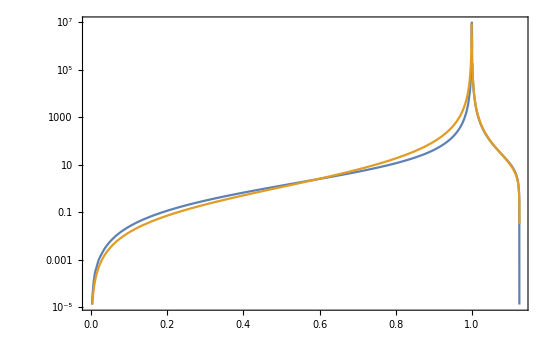

```mathematica
LogPlot[{dePrivFn["PT",EcFn,λbar],dePrivFn["PT",EcAn,λbar]},{λbar,0,9/8},Frame->True]
```

The action is S_E=Φ_b^2/(M T)(Ē)_c. For the exact expression for (Ē)_c(λ̄), let’s plot it as a function of θ=T/T_c for varying Δ parameters:

```mathematica
Clear[μ,Δ,A,λ]

fullSE=(((((dePrivFn["PT",Fb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcFn,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.T->Tc*θ)//FullSimplify;
```

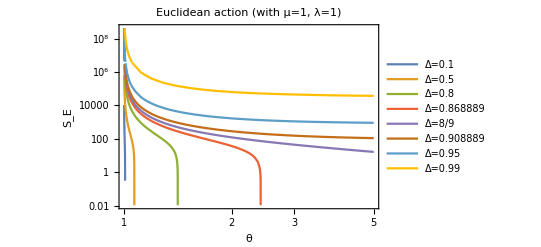

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity Which[0≤Indeterminate<0.00001,«8»,PhaseTransition`Private`limEcThick[hot][(4 1^2+(3 (Times[«2»]+Times[«2»]) (Times[«2»]+1) 1^2)/Times[«5»]^2)/(4 (1/t)^2)]] encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

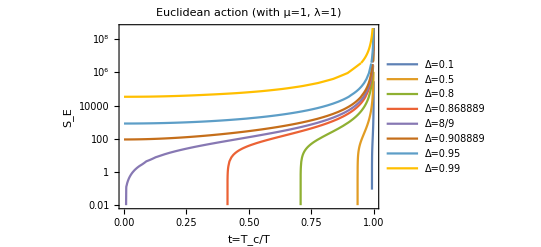

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1,θ->1/t})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

Taking the approximate expression instead:

```mathematica
approxSE=Assuming[ll>0,((((((((dePrivFn["PT",Fb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcAnHot,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.{T->Tc*θ,λ->ll^2})//FullSimplify)/.Abs[θ]->θ)//FullSimplify)]/.ll->√λ
```

(2.33313 (9+(-8+8/θ^2)/Δ-8/θ^2)^(3/4) θ^3 (1. Δ^(3/2) θ+0.333333 Δ √(8-8 θ^2+Δ (-8+9 θ^2)))^2 μ)/((-1.+Δ)^2 (-1.+θ^2)^2 √(-1+Δ+θ^2) λ)

We can see that as Δ→8/9 the allowed temperatures become larger and larger (i.e. it takes longer to hit the spinodal temperature, or λ̄=9/8). Eventually, once Δ>8/9, a non-zero minimum action is reached.

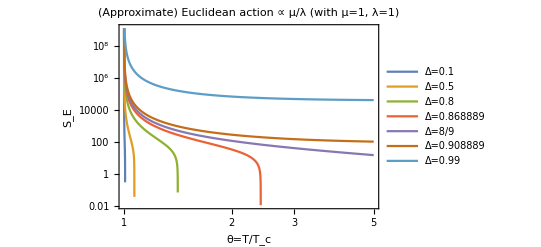

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
(approxSE/.{μ->mu,λ->lam})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

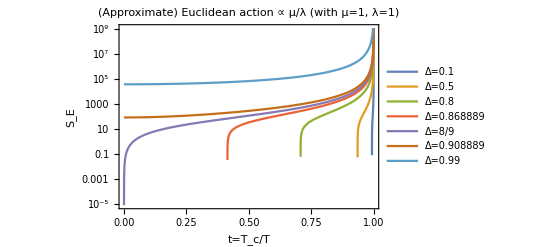

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
Assuming[t>0,(approxSE/.{μ->mu,λ->lam,θ->1/t})//FullSimplify];
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

## Spinodal temperature

λ̄ will reach 9/8 (corresponding to the spinodal temperature) for some temperature θ as long as Δ<8/9, if Δ≥8/9 then λ̄=9/8 is never reached:

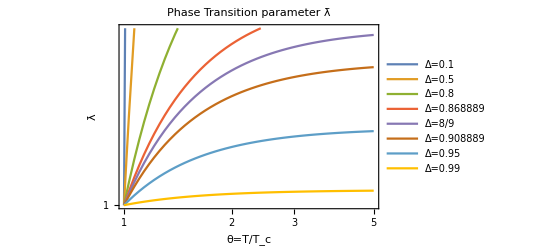

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(λbarRule/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]
Clear[ΔTab]
```

In terms of t=T_c/T:

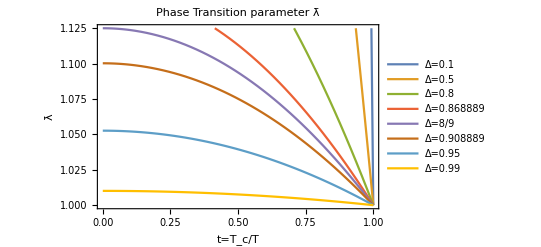

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
((λbarRule/.θ->1/t)/.Δ->#&)/@ΔTab;
Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]

(*Export[PlotsDir<>"lbar_t.pdf",%]*)

Clear[ΔTab]
```

We can then plot Δ(θ) such that λ̄=9/8:

λ̄=(-1+Δ+θ^2)/(Δ θ^2)

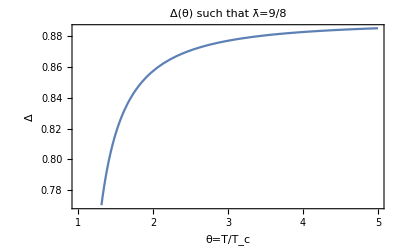

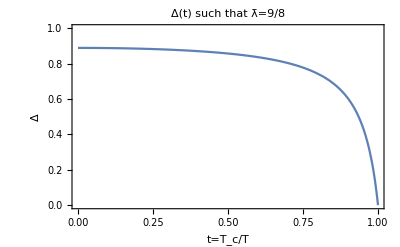

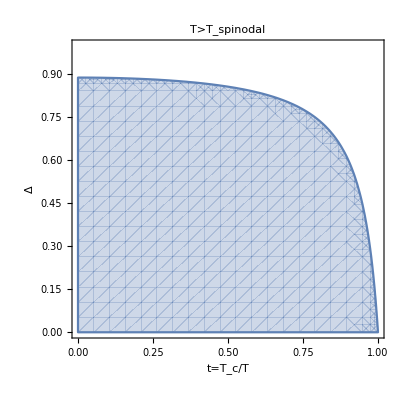

(8 (-1+t^2))/(-9+8 t^2)

```mathematica
lbar=λbarRule;

Print["λ̄=",lbar]
Δ/.(Solve[lbar==9/8,Δ]//Flatten);
Plot[%,{θ,1,5},Frame->True,FrameLabel->{"θ=T/T_c","Δ"},PlotLabel->"Δ(θ) such that λ̄=9/8"]
%%/.θ->1/t;
Plot[%,{t,0,1},Frame->True,FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"Δ(t) such that λ̄=9/8",PlotRange->{{0,1},{0,1}}]

RegionPlot[(lbar/.θ->1/t)>9/8,{t,0,1},{Δ,0,1},FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"T>T_spinodal"]
(*Export[PlotsDir<>"spinodal_t-Delta.pdf",%]*)

(lbar/.θ->1/t)//Simplify;
(Δ/.Solve[%==9/8,Δ]//Flatten)⟦1⟧

Clear[lbar]
```

## Daisy contributions

Daisy contributions from a boson scale like ~N g T, where N is some number associated to the degeneracy of the boson in question. The normal contribution to A scales like ~N g⟨Φ⟩. We then need to compare T/⟨Φ⟩. This factor seems to be irrelevant for most values of Δ as well as for most temperatures, up to and including the spinodal temperature (θ_s=√((8-8Δ)/(8-9Δ))).

The ratio (T/Φ_b)^2 is then given by:

```mathematica
(((((((T/dePrivFn["PT",Fb]/.dePrivFn["PT",PotToCoeffs])/.dePrivFn["PT",TToλbarΔ])/.dePrivFn["PT",ARule])//Simplify//FullSimplify)/.λ->λ^2)//Simplify)/.λ->λ^(1/2))//Simplify;
DaisyRatio=%^2
```

(4 λ)/(3 Δ (3+√(9-8 λbar))^2 μ^2)

(9-8 t^2)/(54-54 t^2)

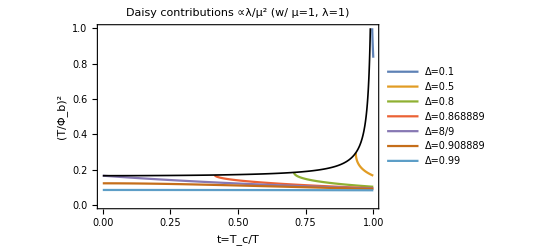

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};

daisy=(DaisyRatio/.{λbar->λbarRule})/.{μ->mu,λ->lam,θ->1/t};
Table[daisy,{Δ,ΔTab}];

p1=Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","(T/Φ_b)^2"},PlotRange->{0,1},PlotLabel->StringForm["Daisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",mu,lam]];

(Δ/.(Solve[λbarRule==9/8,Δ]//Flatten))/.θ->1/t;
Assuming[t>0,(daisy/.Δ->%)//FullSimplify]
p2=Plot[%,{t,0,1},PlotStyle->{Thickness[0.003],Black},PlotRange->{0,1}];
Show[p1,p2]

(*Export[PlotsDir<>"daisies_t.pdf",%]*)

Clear[ΔTab,daisy,mu,lam,p1,p2]
```

Same as above, but instead plotting the correction to the cubic coefficient (1+(T/Φ_b)^2)^(3/2)-1:

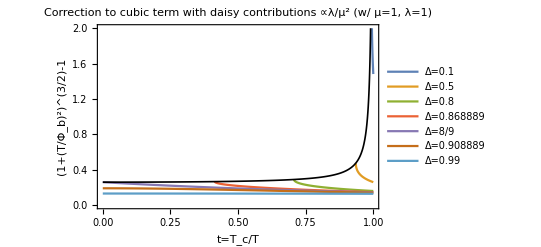

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};

daisy=(DaisyRatio/.{λbar->λbarRule})/.{μ->mu,λ->lam,θ->1/t};
Table[(1+daisy)^(3/2)-1,{Δ,ΔTab}];

p1=Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","(1+(T/Φ_b)^2)^(3/2)-1"},PlotRange->{0,2},PlotLabel->StringForm["Correction to cubic term with\ndaisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",mu,lam]];

(Δ/.(Solve[λbarRule==9/8,Δ]//Flatten))/.θ->1/t;
Assuming[t>0,(((1+daisy)^(3/2)-1)/.Δ->%)//FullSimplify];
p2=Plot[%,{t,0,1},PlotStyle->{Thickness[0.003],Black},PlotRange->{0,2}];
Show[p1,p2]

(*Export[PlotsDir<>"daisies_t.pdf",%]*)

Clear[ΔTab,daisy,mu,lam,p1,p2]
```

(4 λ)/(3 Δ (3+√(9-8 λbar))^2 μ^2)

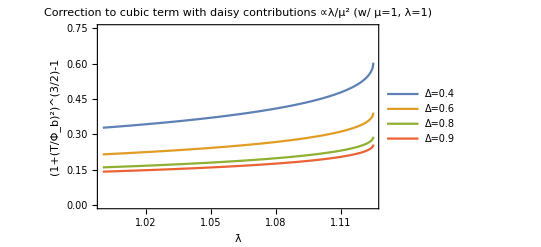

```mathematica
daisy=DaisyRatio

Table[{(1+daisy)^(3/2)-1}/.{λ->1,μ->1},{Δ,{0.4,0.6,0.8,0.9}}];

Plot[%,{λbar,1,9/8},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@{0.4,0.6,0.8,0.9}),FrameLabel->{"λ̄","(1+(T/Φ_b)^2)^(3/2)-1"},PlotRange->{0,0.75},PlotLabel->StringForm["Correction to cubic term with\ndaisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",1,1]]

Clear[daisy]
```

```mathematica
Clear[DaisyRatio]
```

## Runaway condition

The runaway condition is

sign[1-λ̄]((-V_(b,0))-μ^2/2 T^2 Φ_b^2)>0, or alternatively

(-V_(b,0))/(μ^2/2 T^2 Φ_b^2)>1 for λ̄<1 (cPT) .

(-V_(b,0))/(μ^2/2 T^2 Φ_b^2)<1 for λ̄>1 (hPT) .

```mathematica
num=-(dePrivFn["PT",Vb0]/.dePrivFn["PT",PotToCoeffs0Temp])/.dePrivFn["PT",ARule]

den=((((μ^2/2(T*dePrivFn["PT",Fb])^2)/.dePrivFn["PT",PotToCoeffs])/.dePrivFn["PT",ARule])/.dePrivFn["PT",TToλbarΔ])//FullSimplify

condition=num/den
```

(3 Tc^4 (-1+Δ)^2 μ^4)/(2 λ)

(3 Tc^4 (-1+Δ)^2 Δ (9+3 √(9-8 λbar)-4 λbar) μ^4)/(4 λ (-1+Δ λbar)^2)

(2 (-1+Δ λbar)^2)/(Δ (9+3 √(9-8 λbar)-4 λbar))

Runaway for hPT (note that when Δ≥8/9 the condition becomes zero for some λ̄<9/8, for which T→∞ because the spinodal temperature does not exist), and also for cPT.

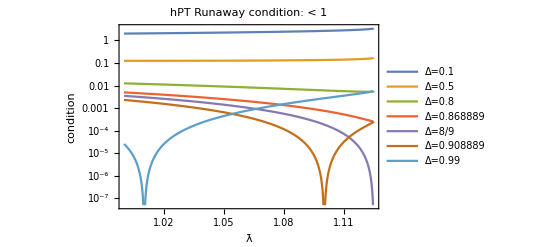

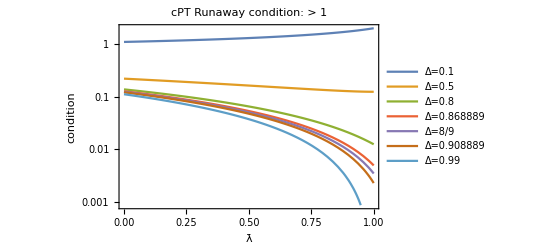

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
condition=Table[condition/.Δ->Δval,{Δval,ΔTab}];

LogPlot[condition,{λbar,1,9/8},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"λ̄","condition"},PlotLabel->"hPT Runaway condition: < 1"]

LogPlot[condition,{λbar,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"λ̄","condition"},PlotLabel->"cPT Runaway condition: > 1"]

Clear[num,den,condition,ΔTab,cond]
```

## Clear

```mathematica
Clear[λbarRule]
```

## Reheating

Exact {x_c1,x_max,x_c2}:

{0.028198578971265894116934197555,0.53158666338798730884034711327,9.2410317267989175514413811419}

Approximate {x_c1,x_max,x_c2}:

{0.0256,0.534187,10.4167}

Error [(Approx-Exact)/Exact]:

{-0.0921528,0.00489109,0.127219}

Domain:

{0,10000.}

γ_c^RATE

{0.2263541772833099700055,-0.2380892768487426571113}

-Graphics-

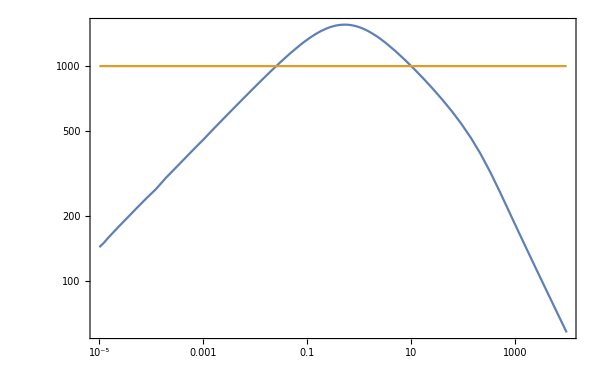

```mathematica
gam=0.01;
regime=If[gam≤1,"γ<<1","γ>>1"];

eff=Max[2.5/gam^(1/4),2];
rcrit=eff^-4;

res=solEqs[gam,0,10^3,40,20];
Print["Exact {x_c1,x_max,x_c2}:"]
xLR=xCross[gam,rcrit]
((dePrivFn["RH",RHDict["xcVals"][regime]])/.{γ->gam,f->eff})//N;
((dePrivFn["RH",RHDict["xMax"][regime]])/.{γ->gam,f->eff})//N;
Print["Approximate {x_c1,x_max,x_c2}:"]
{%%%⟦1⟧,%%,%%%⟦2⟧}
Print["Error [(Approx-Exact)/Exact]:"]
(%%/%%%%%%)-1

Print["Domain:"]
domain=InterpolatingFunctionDomain[res⟦2⟧]//Flatten

Print["γ_c^RATE"]
{gammaRate[gam,xLR⟦1⟧],gammaRate[gam,xLR⟦-1⟧]}

p1=LogLogPlot[{res⟦1⟧[x],res⟦2⟧[x]},{x,10^-5,domain⟦2⟧},PlotRange->{10^-8,100},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->{(xLR)~Join~{1/gam},{rcrit}},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_{\\chi}",Magnification->1.7],MaTeX["\\rho_{r}",Magnification->1.7]}],{0.9,0.85}],Epilog->{Inset[Rotate[MaTeX["\\color{black} t=t_\\textrm{max}",Magnification->1.5],90°],Scaled[{.43,.2}]],Inset[Rotate[MaTeX["\\color{black} t=\\Gamma_\\chi^{-1}",Magnification->1.5],90°],Scaled[{.63,.2}]],Inset[Rotate[MaTeX["\\color{black} T=T_c",Magnification->1.5],0°],Scaled[{.08,.55}]],Inset[Rotate[MaTeX[ToString["\\begin{aligned} \\Gamma_\\chi &= "<>ToString[gam]<>"H_i \\end{aligned}"],Magnification->1.3],0°],Scaled[{.13,.9}]]}];

χDFns={rχ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"χD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"χD"]])}/.{γ->gam,f->eff};
RDFns={rχ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]])}/.{γ->gam,f->eff};
(χDFns~Join~RDFns);

p2=LogLogPlot[%,{x,10^-5,domain⟦2⟧},PlotStyle->{{Blue,Dashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Blue,Dotted,Thickness[0.002]},{Red,Dotted,Thickness[0.002]}},PlotRange->{10^-8,100},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16];

Show[p1,p2]

gSS=10;
TC=1000;
HI=eff^2*(Aρ/.gstar->gSS)*TC^2/(3mpl);
TOfx[gam,gSS,HI,0,10^3,30,20];
LogLogPlot[{%[x],TC},{x,10^-5,domain⟦2⟧},Frame->True,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["T [\\mathrm{GeV}]",Magnification->2]}]

Clear[gam,eff,regime,rcrit,res,xLR,domain,χDFns,RDFns,p1,p2,gSS,TC,HI]
```

## Gravitational Wave Spectra

## Stochastic Gravitational Wave Background from First Order Phase Transition (SGWB from 1PT)

## TODO: ***Analytical Approximations***

## Numeric SGWB

### SGWB spectra formulas

```mathematica
Clear[fenv,Senvf,Ωenv,fsw,Sswf,Ωsw,fturb,fturb,Sturbf,Ωturb,κFn]

(*GW from envelope approximation*)
fenv[β_,vw_]:=Abs[β](0.62/(1.8-0.1vw+vw^2))*GeV/mHz(*[mHz]*);
Senvf[f_,fenv_]:=(3.8 (f/fenv)^2.8)/(1+2.8(f/fenv)^3.8);
Ωenv[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*R^2((κ α)/(1+α))^2*(Hs/β)^2((0.11 vw^3)/(0.42+vw^2))Senvf[f,Z^-1 fenv[β,vw]];

(*GW from sound waves*)
fsw[β_,vw_]:=2/(√3)×β/vw*GeV/mHz(*[mHz]*);
Sswf[f_,fsw_]:=(f/fsw)^3(7/(4+3(f/fsw)^2))^(7/2)
Ωsw[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*0.159*R^2((κ α)/(1+α))^2*(Hs/β)vw Sswf[f,Z^-1 fsw[β,vw]];

(*GW from turbulence*)
fturb[β_,vw_]:=3.5/2×β/vw*GeV/mHz(*[mHz]*);
Sturbf[f_,fturb_,hstar_]:=(f/fturb)^3/((1+f/fturb)^(11/3)(1+8π f/hstar))
Ωturb[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*20.1*R^2((κ α)/(1+α))^2*(Hs/β)vw Sturbf[f,Z^-1 fturb[β,vw],Z^-1 Hs*GeV/mHz];

(*efficiency*)
κFn[vw_,αN_]:=Block[{αn=αN,αmax,α,cs,vwJ,κA,κB,κC,κD,δκ},

αmax=1/3(1-vw)^(-13/10);
α=Min[αN,αmax];
cs=√(1/3);
vwJ=1/(1+α)(√(2/3 α+α^2)+√(1/3));
κA=vw^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB=α^(2/5)/(0.017+(0.997+α)^(2/5));
κC=(√α)/(0.135+√(0.98+α));
κD=α/(0.73+0.083 √α+α);
δκ=-0.9Log[(√α)/(1+√α)];

If[0≤vw≤cs,
(cs^(11/5)κA κB)/((cs^(11/5)-vw^(11/5))κB+vw cs^(6/5)κA),
If[cs<vw<vwJ,
κB+(vw-cs)δκ+(vw-cs)^3/(vwJ-cs)^3(κC-κB-(vw-cs)δκ),
If[vwJ≤vw≤1,
((vwJ-1)^3 vwJ^(5/2)vw^(-5/2)κC κD)/(((vwJ-1)^3-(vw-1)^3)vwJ^(5/2)κC+(vw-1)^3 κD),
Print["Error"]
]
]
]
];
```

### Numeric SGWB from 1PT

```mathematica
Clear[gwSpectra]

gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,gSM,True,0},δxLargePrecAccu_List:{10^-6,10^3,30,20}]:=gwSpectra[gUVs,vwCool,coeffs,Tcrit,Hd,Γχ,method,verbose,hh,KfacΓfull,NlxExpansionSum,IRinstantVSRHwx,δxLargePrecAccu]=Block[{gdUV,gUV,gstar,Tc=Tcrit,Hi=Hd,γd=Γχ/Hd,Kfactor,full,Nlx,expansion,sum,wχ,gdIR,gd0,gIR,instantVSRH,δ,xLarge,prec,accu,xd,t0,rχ,rr,Tx,ax,tx,xDomain,xm,rCrit,xCritBoil,xpk,xCritCool,Tpk,xcs,tcs,TempEvol,gammas,vwboil=1,Tpts,tpts,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,xpts,Hss,Rs,Zs, fullResult,fullResultLabels,spec,tmp},

(*distributing list arguments*)
{gdUV,gUV}=gUVs(*DS & VS UV d.o.f.*);
gstar=gdUV+gUV(*total plasma UV d.o.f.*);

{Kfactor,full}=KfacΓfull(*K-prefactor for Subscript[Γ, nucl]/𝒱; whether (Subscript[S, E]/2π)^(3/2) 0-modes prefactor included*);

{Nlx,expansion,sum}=NlxExpansionSum(* # ln(x) steps; whether Universe expansion considered; whether sum for a(x) and τ̄(x) considered*);

{gdIR,gd0,gIR,instantVSRH,wχ}=IRinstantVSRHwx(*DS d.o.f. in IR; DS-to-VS temperature ratio in IR; VS d.o.f. in IR, VS temperature in IR; whether VS reheated instantaneously; reheaton e.o.s.*);
gdIR=If[gdIR===Automatic,gdUV,gdIR];

{δ,xLarge,prec,accu}=δxLargePrecAccu(*tiny number for derivative computation, largest x-value for reheating story, precision, accuracy*);

(*the reference time, at which the χ-decays start*)
tmp=dePrivFn["RH",xd];
xd=tmp;
t0=xd/Hi;

(*the solutions to the reheating equations*)
{rχ,rr}=solEqs[γd,wχ,xLarge,prec,accu];

(*T(x)*)
Tx=TOfx[γd,gstar,Hi,wχ,xLarge,prec,accu];

(*scale factor a(x), with Subscript[a, ini]=a(x=Subscript[x, d])=1*)
ax=If[expansion==False,1,aOfx[γd,1,sum,wχ,xLarge,prec,accu]];

(*dimensionless comoving time τ̄(x)*)
tx=If[expansion==False,1,tauOfx[γd,1,1,sum,wχ,xLarge,prec,accu]];

(*its time domain*)
xDomain=(InterpolatingFunctionDomain[Tx]//Flatten);

(*deep in DS RD*)
xm=xDomain⟦-1⟧;

(*the dimensionless radiation density at critical temperature*)
rCrit=(Aρ Tc^4)/ρχi;

(*the dimensionless crossing times, at which the radiation density reaches critical temperature*)
{xCritBoil,xpk,xCritCool}=xCross[γd,rCrit,wχ,xLarge,prec,accu];

(*the peak temperature*)
Tpk=Tx[xpk];

(*a handy list for dimensionless crossing times*)
xcs={xCritBoil,xCritCool};

(*the dimensionful critical times*)
tcs=xcs/Hi;

(*reading 'method' argument to find PT temperature*)
If[MemberQ[{"analytic","semi","numeric","alt"},method]==False,Return["Please write argument 'method' a string: either 'analytic', 'semi', 'numeric', or 'alt'."]];

(*computing the PT*)
If[method=="analytic",
(*the power law behavior of the temperature as a function of time*)
gammas=gammaRate[γd,#,wχ,δ,xLarge,prec,accu]&/@xcs;
(*the parameters for the temperature evolution*)
TempEvol=Table[{gammas⟦i⟧,t0,tcs⟦i⟧},{i,2}];
,
(*the arguments for the temperature evolution*)
TempEvol={Tx,1/Hi}&/@{_,_}(*making a copy: for boiling and cooling*);
];

(*finding the properties of the phase transition: a list of pairs; the first entry being the boiling PT, the second the cooling PT*)
(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[Φ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
{Tpts,tpts,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs}={CheckAbort[ptParams[gstar,"hot",vwboil,TempEvol⟦1⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]],
CheckAbort[ptParams[gstar,"cold",vwCool,TempEvol⟦2⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]]}//Transpose;

(*dimensionless times at which the PT took place*)
xpts=tpts*Hi;

(*Hubble scale at the time of GW generation, which we take to be the time of the PT: H_*=Subscript[H, PT]*)
Hss=Hi*√(rχ[#]+rr[#])&/@xpts;

(*correction due to Subscript[ρ, tot] containing a contribution from the reheaton and not only the DS radiation*)
Rs=Table[((1+αns⟦i⟧)/(1+rχ[xpts⟦i⟧]/rr[xpts⟦i⟧])),{i,2}];

(*the extra redshift factor that GW from boiling PT undergo compared to those from cooling PT*)
Zs=redshift[γd,Hi,{#,xm},{gdUV,gUV},{gdIR,gd0,gIR},instantVSRH,wχ,xLarge,prec,accu,False]&/@xpts;

fullResult={xpk/Hi,xpk,Tpk,tcs,xcs,Tpts,tpts,tpts*Hi,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,Hss,Rs,Zs};
fullResultLabels={"t_max=``","x_max=``","T_max=``","t_c=``","x_c=``","T_PT=``","t_PT=``","x_PT=``","λ̄=``","Φ_b=``","ϵ=``","E_c=``","S_E=``","S_E'=``","S_E''=``","Γ/V=``","β_1=``","β_2=``","n_b=``","R_b=``","⟨R⟩=``","β_eff=``","α_∞=``","α_n=``","κ_eff=``","H_*=``","R=``","Z=``"};

(*print the quantities above*)
If[verbose,Print[StringRiffle[Table[StringForm[fullResultLabels⟦i⟧,ScientificForm[fullResult⟦i⟧,4]],{i,Length@fullResult}],"\n"]]];

spec={Ωenv[f,βeffs⟦1⟧,vwboil,Rs⟦1⟧,effs⟦1⟧,αns⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh],Ωsw[f,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κFn[vwCool,αns⟦2⟧],αns⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh]};

Return[spec]
]
```

### Examples

Some examples of parameters that work:

1. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.5, 1}, T_c=500 GeV (—5 TeV), γ=0.2, f=(1.03×1.7/γ^(1/4))
2. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.8, 1}, T_c=200 GeV, γ=0.2 (0.3), f=(1.3×1.7/γ^(1/4))
3. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.1,0.90889, 1.1}, T_c=5 TeV, γ=0.3, f=(3.7×1.7/γ^(1/4))
4. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.5,0.888789, 1}, T_c=5 TeV, γ=0.02, f=(2.2×1.7/γ^(1/4))
5. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1, 0.90889, 1}, T_c=500 GeV (—5 TeV), γ=50, f = 3.5*(1+1/γ^(1/2))

#### Parameters

{μ,A,λ}={1.5,1.22468,1}

T_c exists: True

γ=0.02, f=9.94521

T_c=5000 GeV

T_max=11398.7 GeV

T_s=157206. GeV

{x_c1,x_max,x_c2}={0.005,0.529,37.895}

λ̄(T_max)=1.10105 (if not smaller than 9/8=1.125 then T_s is reached)

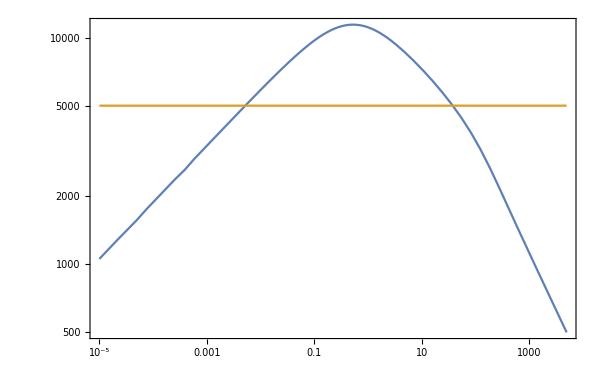

```mathematica
verbose=True;
gDSUV=10;
gVSUV=0.(*106.75*);
gs=gDSUV+gVSUV;
vwc=0.05;

(*
(*VERY STRONG 1PT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)
μ=1.5;
λ=1;
(*Δ=8/9+0.01;*)
(*Δ=8./9+0.0001;*)
(*Δ=0.95;*)
Δ=8/9-0.0001;
(*Δ=0.89;*)
(*Δ=0.85;*)
(*Δ=0.75;*)
(*Δ=0.5;*)
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=5000GeV;

gam=0.02;
regime=If[gam≤1,"γ<<1","γ>>1"];
(*Print["f∈[",((dePrivFn["RH",RHDict["fmin"][regime]])/.γ->gam)//N,", ",(fMax[regime]/.γ->gam)//N,"]"]*)
eff=If[regime=="γ<<1",2.2*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["γ=",gam,", f=",eff]

solEqs[gam];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);Gam=gam*Hdec;

Tofx=TOfx[Gam/Hdec,gs,Hdec];
Hofx=HOfx[Gam/Hdec,Hdec];
dlnTdt[x_]=Hdec*D[Tofx[x],x]/Tofx[x];
d2lnTdt2[x_]=Hdec*D[dlnTdt[x],x];

domain=InterpolatingFunctionDomain[Tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=Tofx[xMAX];

Print["T_c=",Tcr, " GeV"]
Print["T_max=",Tmx," GeV"]
Print["T_s=",(Ts/.dePrivFn["PT",Tspinodal])/.Tc->Tcr, " GeV"]
Print["{x_c1,x_max,x_c2}=",Round[#,0.001]&/@{xC1,xMAX,xC2}]
Print["λ̄(T_max)=",(dePrivFn["PT",λbar]/.dePrivFn["PT",McλbarToCoeffs])/.{Tc->Tcr,T->Tmx}," (if not smaller than 9/8=1.125 then T_s is reached)"]


LogLogPlot[{Tofx[x],Tcr},{x,10^-5,domain⟦-1⟧},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\mathrm{Temperature}\\ [\\mathrm{GeV}]",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["T_\\mathrm{rh}(x)",Magnification->1.7],MaTeX["T_\\mathrm{c}",Magnification->1.7]}],{0.9,0.85}]]
```

#### PT quantities

```mathematica
SE2Max=S2Rate[dlnTdt[xMAX],d2lnTdt2[xMAX],pars,Tcr,Tmx];

GV=(Γnucl[pars,Tcr,Tofx[xMAX],1,False]);
GV0m=(Γnucl[pars,Tcr,Tofx[xMAX],1,True]);
n0=(√(2π))/(√SE2Max)GV;
n00m=(√(2π))/(√SE2Max)GV0m;


(*Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]*)
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr]),", S_E(T_max)/(4×ln[T_c/H_dec])=",SETemp[pars,Tcr,Tmx]/(4Log[Tcr/Hdec])]
Print["S_E''(T_max)=",SE2Max]
Print["√S_E/H_dec=",√SE2Max/Hdec,", √S_E/Γ_dec=",√SE2Max/Gam]
Print["dS/dlnT(T_max)=",dePrivFn["PT",dSdlnT,pars,Tcr,Tmx]]
Sqrt[Abs[dePrivFn["PT",dSdlnT,pars,Tcr,Tmx]]]

dePrivFn["PT",dSdlnT,pars,Tcr,(*Tcr(1+(Δ^(5/4)√(μ/λ))/((1-Δ)√(4Log[Tcr/Hdec])))*)Tmx];
%*dlnTdt[xC1]/Hdec
Sqrt[%%*d2lnTdt2[xMAX]/Hdec^2]

Print[""]
Print["**********************"]
Print["For supracritical 1PT:"]

{Tptn0,tptn0,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,False,{1,1},250];

Print["............"]
Print["w/o 0-modes:"]
Print["n_0 = ",n0,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n0 1^3)^(1/3)]
Print["x_PT=",Round[tptn0*Hdec,0.001]]
Print["T_PT=",Tptn0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]
Print["(t_PT-t_max)·√S_E=",(tptn0-xMAX/Hdec)*√SE2Max]
Print["(t_PT-t_max)·β_eff=",(tptn0-xMAX/Hdec)*beff]
Print["β_eff/H_dec=",beff/Hdec,", β_eff/Γ_dec=",beff/Gam]
Print["S_E=",SEu,", S_(E, appx)=",4Log[Tcr/Hdec],", S_E/S_(E, appx)=",SEu/(4Log[Tcr/Hdec])]
Print["S_E'=",SE1,", S_(E, appx)'=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))]
Print["S_E'/β_eff=",SE1/beff,", S_E'/H_dec=",SE1/Hdec,", S_(E, appx)'/H_dec=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))/Hdec]

{Tptw0,tptw0,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,True,{1,1},250];

Print["............"]
Print["w/ 0-modes:"]
Print["n_0 = ",n00m,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n00m 1^3)^(1/3)]
Print["x_PT=",Round[tptw0*Hdec,0.001]]
Print["T_PT=",Tptw0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]
Print["(t_PT-t_max)·√S_E=",(tptw0-xMAX/Hdec)*√SE2Max]
Print["(t_PT-t_max)·β_eff=",(tptw0-xMAX/Hdec)*beff]
Print["β_eff/H_dec=",beff/Hdec,", β_eff/Γ_dec=",beff/Gam]
Print["S_E=",SEu,", S_(E, appx)=",4Log[Tcr/Hdec],", S_E/S_(E, appx)=",SEu/(4Log[Tcr/Hdec])]
Print["S_E'=",SE1,", S_(E, appx)'=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))]
Print["S_E'/β_eff=",SE1/beff,", S_E'/H_dec=",SE1/Hdec,", S_(E, appx)'/H_dec=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))/Hdec]

Clear[λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,GV0m,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff]
```

S_E(T_max)=125.991

S_E(T_max)/(4×ln[m_Pl/T_c])=0.93135, S_E(T_max)/(4×ln[T_c/H_dec])=1.07946

S_E''(T_max)=1.78069×10^-16

√S_E/H_dec=12.5505, √S_E/Γ_dec=627.524

dS/dlnT(T_max)=-331.206

18.1991

-15591.4

12.5513

**********************

For supracritical 1PT:

............

w/o 0-modes:

n_0 = 6.08212×10^-31,  (8π·n_0·v_w^3)^(1/3) = 2.48179×10^-10

x_PT=8.323

T_PT=7600.46 GeV

n_b = 6.10007×10^-31,  β_eff = 2.48423×10^-10

(t_PT-t_max)·√S_E=97.8194

(t_PT-t_max)·β_eff=1.82105

β_eff/H_dec=0.233646, β_eff/Γ_dec=11.6823

S_E=505.626, S_(E, appx)=116.717, S_E/S_(E, appx)=4.33209

S_E'=7.47194×10^-8, S_(E, appx)'=-0.0000138004

S_E'/β_eff=300.775, S_E'/H_dec=70.2749, S_(E, appx)'/H_dec=-12979.5

............

w/ 0-modes:

n_0 = 5.46127×10^-29,  (8π·n_0·v_w^3)^(1/3) = 1.11133×10^-9

x_PT=2.276

T_PT=9984.37 GeV

n_b = 5.509×10^-29,  β_eff = 1.11456×10^-9

(t_PT-t_max)·√S_E=21.9298

(t_PT-t_max)·β_eff=1.83166

β_eff/H_dec=1.04827, β_eff/Γ_dec=52.4133

S_E=182.77, S_(E, appx)=116.717, S_E/S_(E, appx)=1.56593

S_E'=4.3452×10^-8, S_(E, appx)'=-0.0000138004

S_E'/β_eff=38.9857, S_E'/H_dec=40.8674, S_(E, appx)'/H_dec=-12979.5

#### 1PT evolution

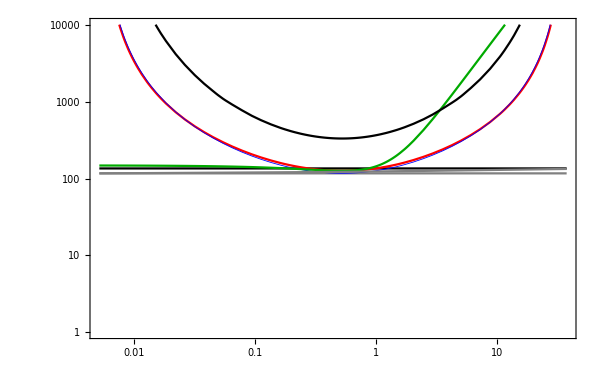

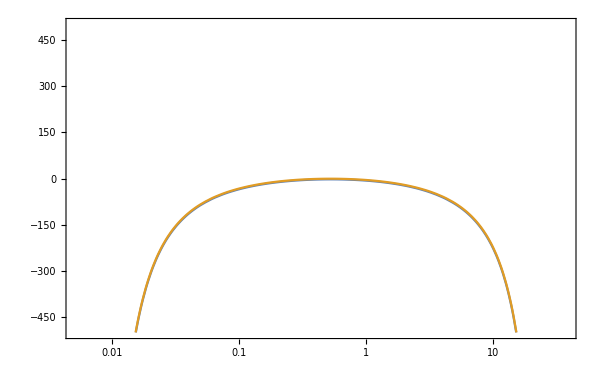

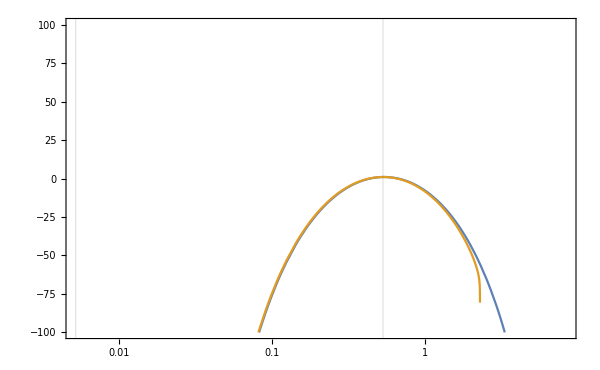

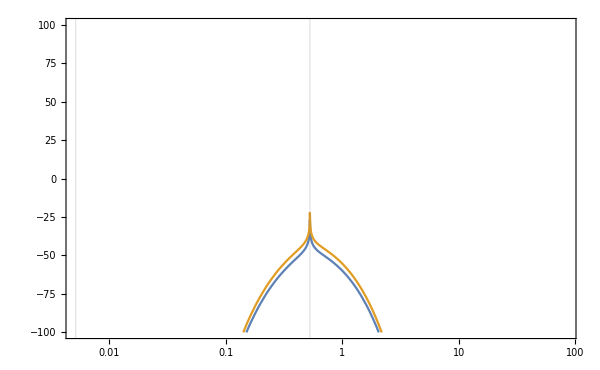

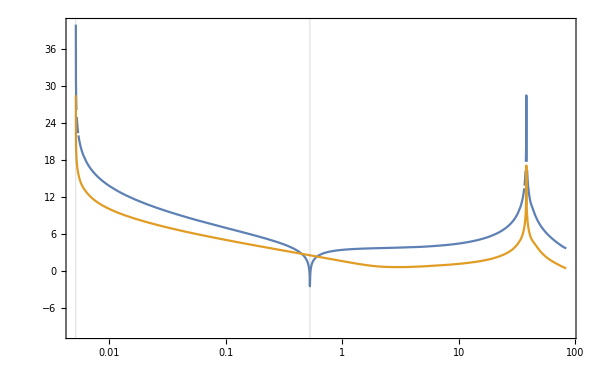

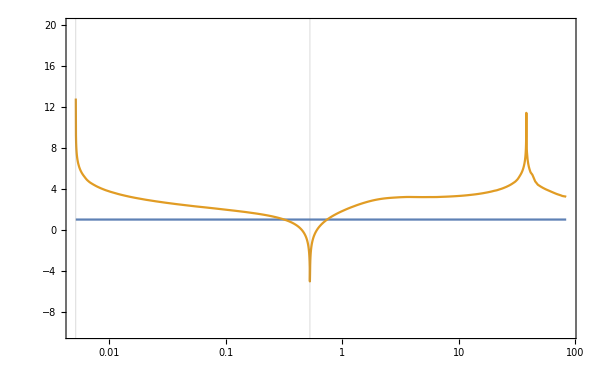

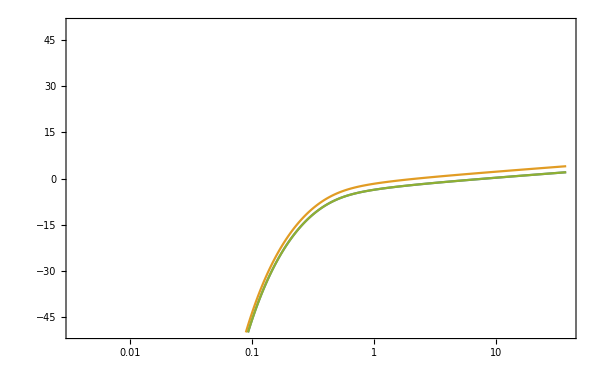

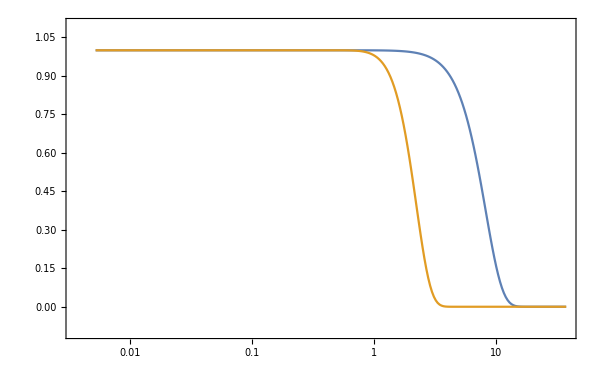

```mathematica
DS=(Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]/dlnTdt[x]]);

LogLogPlot[{4Log[mpl/Tcr],4Log[Tcr/Hdec],SETemp[pars,Tcr,Tofx[x]],approxSE/.{θ->(Tofx[x]/Tcr)},SETemp[pars,Tcr,Tofx[xMAX]]+SE2Max*1/2(x-xMAX)^2*Hdec^-2,DS,4Log[Tofx[x]/Hofx[x]]},{x,xC1,xC2},Frame->True,PlotRange->{1,10^4},PlotStyle->{Black,Gray,Red,{Blue,Thickness[0.001]},Darker@Green},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["S_\\mathrm{E}",Magnification->2]},PlotLabel->MaTeX["\\text{Euclidean Action}",Magnification->1.7],PlotLegends->Placed[LineLegend[{MaTeX["4 \\ln(m_\\mathrm{Pl}/T_\\mathrm{c})",Magnification->1],MaTeX["4 \\ln(T_\\mathrm{c}/H_\\mathrm{dec})",Magnification->1],MaTeX["S_E(x)",Magnification->1],MaTeX["S_E^\\mathrm{ appx.}(x)",Magnification->1],MaTeX["S_E^{\\prime\\prime}(t-t_\\mathrm{max})^2 /2",Magnification->1]}],{0.2,0.25}]]
(*Export[PlotsDir<>"SE_x.pdf",%]*)

LogLinearPlot[{Γnucl[pars,Tcr,Tofx[x],1,False,True]-4Log10[Hdec],Γnucl[pars,Tcr,Tofx[x],1,True,True]-4Log10[Hdec]},{x,xC1,xC2},Frame->True,PlotRange->{-500,500},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H_\\mathrm{dec}^4)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.7],MaTeX["\\text{w/ 0-modes}",Magnification->1.7]}],{0.8,0.85}]]

LogLinearPlot[{Log[4/3 π*1^3(x)((tptn0*Hdec)-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True]*Log[10]+4Log[Tcr/Hdec],Log[4/3 π*1^3(x)((tptw0*Hdec)-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True]*Log[10]+4Log[Tcr/Hdec]},{x,xC1,(Max[tptn0,tptw0]*Hdec)},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[J(x_{\\rm PT},x')]",Magnification->2]},PlotLabel->MaTeX["\\text{Origin of Bubbles}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{Log[8π*1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]],Log[8π*1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\mathrm{cond}(x)]",Magnification->2]},PlotLabel->MaTeX["\\text{1PT condition}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/Hdec],Log[√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]]/Hdec]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-10,40},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{1,Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]]]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-10,20},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX},None}]


(*h(x) w/o scale factor*)
Lmlnh1=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},250];

(*Subscript[n, b](x) w/o scale factor*)
LnbLx=Lnbubble[Lmlnh1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1}];
xData=(InterpolatingFunctionCoordinates[LnbLx]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten);
LnbLx={(10^xData),10^yData}//Transpose;

xData=(InterpolatingFunctionCoordinates[Lmlnh1]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh1]//Flatten);
Lmlnh1={(10^xData),yData}//Transpose;

Lmlnh2=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,True,{1,1},250];

xData=(InterpolatingFunctionCoordinates[Lmlnh2]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh2]//Flatten);
Lmlnh2={(10^xData),yData}//Transpose;

Lmlnh3=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},500];
xData=(InterpolatingFunctionCoordinates[Lmlnh3]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh3]//Flatten);
Lmlnh3={(10^xData),yData}//Transpose;

ListLogLinearPlot[{Lmlnh1,Lmlnh2,Lmlnh3},Joined->True,PlotRange->{-50,50},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10} (-\\ln h(x))",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2],MaTeX["\\text{w/o 0-modes; more steps}",Magnification->1.2]}],{0.3,0.75}]]

Lmlnh1=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh2);

ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.2,0.15}],GridLines->{{xMAX - 2/3}~Join~{tptn0*Hdec - 2/3}~Join~{tptw0*Hdec - 2/3},{1/E}}]

Lmlnh1=({#⟦1⟧,#⟦2⟧}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,#⟦2⟧}&/@Lmlnh2);

p1=ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["t H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.8,0.85}],GridLines->{{xMAX }~Join~{tptn0*Hdec}~Join~{tptw0*Hdec - 2/3},{1/E}}];
p2=LogLinearPlot[{Exp[-(4π)/3*(n0/Hdec^3)*1^3*(x-xMAX)^3],Exp[-(4π)/3*(n00m/Hdec^3)*1^3*(x-xMAX)^3]},{x,Lmlnh1⟦1,1⟧,Lmlnh1⟦-1,1⟧},PlotStyle->{Darker@Green,Red},PlotRange->{-0.1,1.1},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes; analytic, simultaneous}",Magnification->1.2],MaTeX["\\text{w 0-modes; analytic, simultaneous}",Magnification->1.2]}],{0.7,0.65}]];
Show[p1,p2]
```

#### SGWB

```mathematica
?gwSpectra
```

StringForm::string: String expected at position StandardForm[Short[Shallow[HoldForm[1], {10, 50}], 5]] in StandardForm[Short[Shallow[HoldForm[StringForm[fullResultLabels[[i]], ScientificForm[fullResult[[i]], 4]]], {10, 50}], 5]].

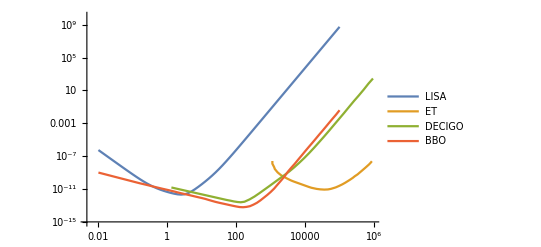

```mathematica
ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotLegends->{"LISA","ET","DECIGO","BBO"},PlotRange->{10^-15,10^10}]
```

*****************

No 0-modes:

.................

t_max=4.976*10^8
x_max=5.290*10^-1
T_max=1.14*10^4
t_c={4.895*10^6, 3.564*10^10}
x_c={5.205*10^-3, 3.790*10^1}
T_PT={7.6*10^3, 2.538*10^3}
t_PT={7.828*10^9, 1.92*10^11}
x_PT={8.323, 2.041*10^2}
λ̄={1.071, 6.394*10^-1}
Φ_b={3.404*10^4, 1.545*10^4}
ϵ={5.242*10^15, 4.637*10^14}
E_c={3.843*10^6, 2.717*10^5}
S_E={5.056*10^2, 1.071*10^2}
S_E'={7.472*10^-8, -1.395*10^-9}
S_E''={8.462*10^-18, 2.136*10^-20}
Γ/V={8.562*10^-205, 1.303*10^-33}
β_1={-7.484*10^-8, 1.385*10^-9}
β_2={-8.449*10^-18, -2.131*10^-20}
n_b={6.1*10^-31, 5.758*10^-25}
R_b={1.179*10^10, 1.202*10^8}
⟨R⟩={7.823*10^9, 7.816*10^9}
β_eff={2.484*10^-10, 1.218*10^-9}
α_∞={6.861, 1.267*10^1}
α_n={5.347*10^-3, 4.301*10^-1}
κ_eff={1.282*10^3, -2.846*10^1}
H_*={7.756*10^-11, 2.831*10^-12}
R={1.031*10^-1, 1.369}
Z={1.215*10^17, 1.792*10^16}

*****************

With 0-modes:

.................

t_max=4.976*10^8
x_max=5.290*10^-1
T_max=1.14*10^4
t_c={4.895*10^6, 3.564*10^10}
x_c={5.205*10^-3, 3.790*10^1}
T_PT={9.984*10^3, 2.557*10^3}
t_PT={2.141*10^9, 1.89*10^11}
x_PT={2.276, 2.009*10^2}
λ̄={1.094, 6.469*10^-1}
Φ_b={4.28*10^4, 1.552*10^4}
ϵ={1.997*10^16, 4.665*10^14}
E_c={1.825*10^6, 2.846*10^5}
S_E={1.828*10^2, 1.113*10^2}
S_E'={4.345*10^-8, -1.46*10^-9}
S_E''={4.218*10^-18, 2.279*10^-20}
Γ/V={6.559*10^-62, 1.477*10^-33}
β_1={-4.341*10^-8, 1.43*10^-9}
β_2={-4.193*10^-18, -2.27*10^-20}
n_b={5.509*10^-29, 5.535*10^-25}
R_b={2.628*10^9, 1.218*10^8}
⟨R⟩={2.136*10^9, 7.668*10^9}
β_eff={1.115*10^-9, 1.202*10^-9}
α_∞={6.283, 1.26*10^1}
α_n={1.795*10^-3, 4.171*10^-1}
κ_eff={3.498*10^3, -2.92*10^1}
H_*={2.398*10^-10, 2.879*10^-12}
R={3.201*10^-2, 1.353}
Z={2.54*10^17, 1.807*10^16}

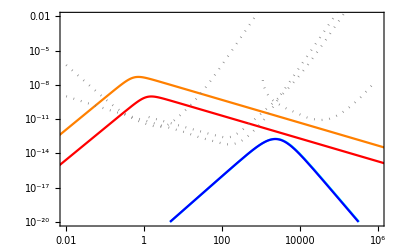

{(4.93453×10^-7 f^2.8)/(1+10.1137 f^3.8),1.26026×10^-20 f^3 (1/(4+5.2719×10^-7 f^2))^(7/2),(1.12616×10^-9 f^2.8)/(1+0.555491 f^3.8),1.29554×10^-20 f^3 (1/(4+5.505×10^-7 f^2))^(7/2)}

```mathematica
(*gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:0.67,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,106.75,True,0},δxLargePrecAccu_List:{1/1000000,1000,30,20}]*)

IRs={Automatic,0,gSM,True,0};

Print["*****************"]
Print["No 0-modes:"]
Print["................."]
gwS=gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,False},{250,False,True},IRs,{10^-6,10^3,30,20}];
Print["*****************"]
Print["With 0-modes:"]
Print["................."]
gwS=gwS~Join~gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^3,30,20}];

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Orange,Cyan,Red,Blue},Frame->True,PlotRange->(*All*){{0.01,10^6},{10^-20,0.01}},PlotLegends->Placed[LineLegend[{MaTeX["\\text{Hot, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Hot, w/ 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/ 0-modes}",Magnification->1.2]}],{0.3,0.15}]];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]
(*Export[PlotsDir<>"sgwb.pdf",%]*)

gwS
```

## ***Scratch***